```mathematica
location = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest2/1024/0.01/";
nMax = 18;
dataTable = Range[nMax];
For[i=17, i<nMax, i++, u=Import[location<>ToString[i]<>"/typeStats.dat", "Data" ]; ListDensityPlot[u, ColorFunction->"GrayTones", ImageSize->{1024,1024}, FrameLabel->{"Time/Arb. Units", "Lattice Position"}, LabelStyle->Large, PlotLegends->Automatic, PerformanceGoal->"Quality"]  //Print]
```

-Graphics-

```mathematica
~
```

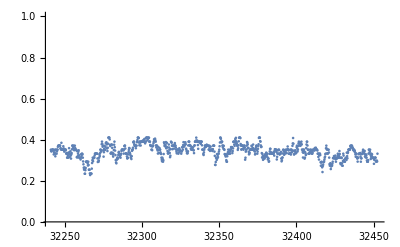

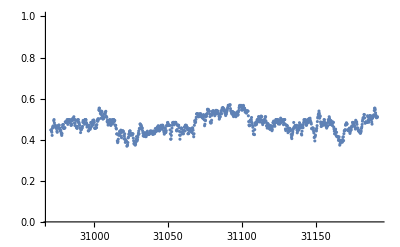

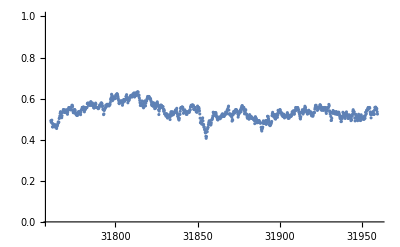

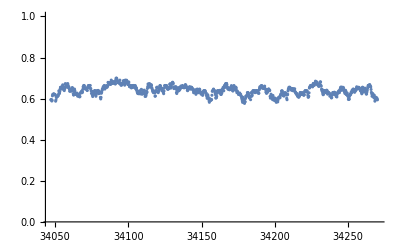

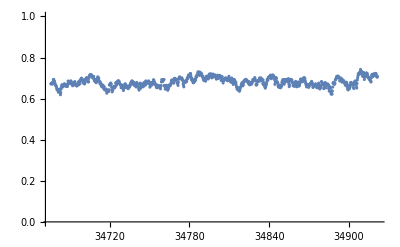

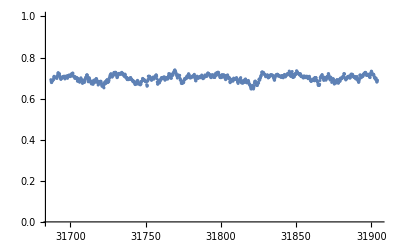

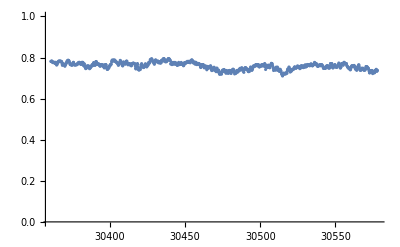

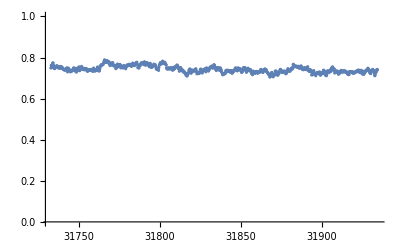

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest3/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/numBonds.dat", "Data" ]; ListPlot[u, PlotRange->{0.0, 1.0}] //Print]
```

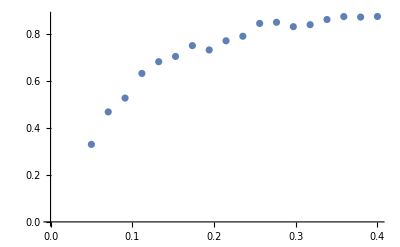

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest3/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/extraInfo.dat", "Data" ]; dataTable[[i+1]] = {u[[1]][[1]], u[[1]][[3]]}];
ListPlot[dataTable]
```